```mathematica
P[i_,t_] := 1/N +  2/N *Sum[
Cos[(i-1/2)*   Pi * k / N ] * Cos[  Pi * k / N/2 ] ^ (2*t +1),
{k, 1, N-1}
]
```

```mathematica
D[P[i,t], t]
```

(2 ∑_(k=1)^(-1+N) 2 Cos[(k π)/(2 N)]^(1+2 t) Cos[((-1/2+i) k π)/N] Log[Cos[(k π)/(2 N)]])/N

```mathematica
T[x_, t_] := Integrate[Cos[(x-1/2)k]*Cos[k/2*(2t+1)], {k, 0, π}]
T[x,t]
```

1/2 (Sin[π (1+t-x)]/(1+t-x)+Sin[π (t+x)]/(t+x))

```mathematica
T[1,0]
```

π/2

```mathematica
(-1-2 t+ⅇ^(π (1/2+t)) ((1-2 x) Cos[π x]+(1+2 t) Sin[π x]))/(1+2 t (1+t)+2 (-1+x) x)
```

(-1-2 t+ⅇ^(π (1/2+t)) ((1-2 x) Cos[π x]+(1+2 t) Sin[π x]))/(1+2 t (1+t)+2 (-1+x) x)

```mathematica
T[1,0]* 2/Pi
```

1

```mathematica
T[x,t]* 2/Pi
```

(Sin[π (1+t-x)]/(1+t-x)+Sin[π (t+x)]/(t+x))/π

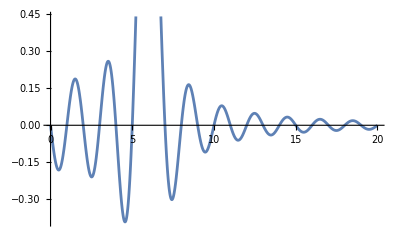

```mathematica
Plot[ Evaluate[T[x,5]], {x, 0, 20}]
```

```mathematica
"交互式绘图"%28DynamicModule[{xc,dx},Manipulate[Plot[Evaluate[T[x,t]],{x,xc-dx,xc+dx}],{{xc,5,"中心"},-25,35},{{dx,5.,"缩放"},30,0.3}],DynamicModuleValues:>{}]
```

```mathematica
P[1,0]  // Simplify
P[2, 0]// Simplify
P[1, 1] // Simplify
P[2, 1]// Simplify
```

1

0

3/4

1/4

```mathematica
P[x,t]
```

1/N+(2 ∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(1+2 t) Cos[(k π (-1/2+x))/N])/N

```mathematica
P[x, t+1] - P[x,t] // Simplify
```

-(2 (∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(1+2 t) Cos[(k π (-1/2+x))/N]-∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(1+2 (1+t)) Cos[(k π (-1/2+x))/N]))/N

```mathematica
Simplify[∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(1+2 t) Cos[(k π (-1/2+x))/N]-∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(1+2 (1+t)) Cos[(k π (-1/2+x))/N]]
```

```mathematica
∑_(k=1)^(-1+N) (Cos[(k π)/(2 N)]^(1+2 t) Cos[(k π (-1/2+x))/N]-Cos[(k π)/(2 N)]^(1+2 (1+t)) Cos[(k π (-1/2+x))/N])
```

$Aborted

```mathematica
Cos[(k π)/(2 N)]^(1+2 t) Cos[(k π (-1/2+x))/N]-Cos[(k π)/(2 N)]^(1+2 (1+t)) Cos[(k π (-1/2+x))/N]
```

```mathematica
Cos[(k π)/(2 N)]^(1+2 t) Cos[(k π (-1/2+x))/N]-Cos[(k π)/(2 N)]^(1+2 (1+t)) Cos[(k π (-1/2+x))/N]// Simplify
```

Cos[(k π)/(2 N)]^(1+2 t) Cos[(k π (-1/2+x))/N] Sin[(k π)/(2 N)]^2

```mathematica
Integrate[2/Pi*Cos[κ/2]^(1+2 t) Cos[ (-1/2+x)κ] Sin[κ/2]^2, {κ, 0, Pi}]
```

$Aborted

```mathematica
Pdiff[x_, t_] := ∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(1+2 t) Cos[(k π (1/2))/N] Sin[(k π)/(2 N)]^2
```

-(2 ∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(2+2 t) Sin[(k π)/(2 N)]^2)/N

```mathematica
Cos[κ/2]^(1+2 t) Cos[ (-1/2+x)κ] Sin[κ/2]^2 + Cos[(π-κ)/2]^(1+2 t) Cos[ (-1/2+x)(π-κ)] Sin[(π - κ)/2]^2 // Expand
```

Cos[(π-κ)/2]^(1+2 t) Cos[(-1/2+x) (π-κ)] Sin[(π-κ)/2]^2+Cos[κ/2]^(1+2 t) Cos[(-1/2+x) κ] Sin[κ/2]^2

```mathematica
f[κ_, x_, t_] := Cos[κ/2]^(1+2 t) Cos[ (-1/2+x)κ] Sin[κ/2]^2
```

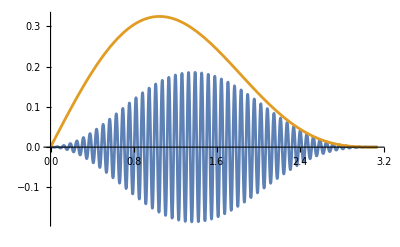

```mathematica
Plot[{Evaluate[f[κ,100,1]], Sin[κ/2] Cos[κ/2]^(1+2*1)}, {κ, 0, Pi}]
```

```mathematica
f[1,2,t]
```

Cos[1/2]^(1+2 t) Cos[3/2] Sin[1/2]^2

```mathematica
Pdiff[1,1]
```

1/64 (-4+4 N-Cos[((-1+N) π)/(2 N)] Csc[π/(2 N)]-Cos[((1+N) π)/(2 N)] Csc[π/(2 N)]+2 Cos[((-2+N) π)/(2 N)] Csc[π/N]-2 Cos[((2+N) π)/(2 N)] Csc[π/N]+Cos[((-3+N) π)/(2 N)] Csc[(3 π)/(2 N)]+Cos[((3+N) π)/(2 N)] Csc[(3 π)/(2 N)])

```mathematica
Integrate[
2/Pi*Cos[κ/2]^(1+2 t) Cos[ (-1/2+y)κ] Sin[κ/2]^2, {κ, 0, Pi}, 
Assumptions->(Element[t, PositiveIntegers] && Element[y, PositiveIntegers])
]
```

```mathematica
Integrate[
Cos[κ/2]^(1+2 t)  Sin[κ/2]^2, {κ, 0, Pi}, 
Assumptions->(Element[t, PositiveIntegers] )
]
```

(√π Gamma[1+t])/(2 Gamma[5/2+t])

```mathematica
∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(1+2 t)
```

```mathematica
Sum[ Cos[(k π)/(2 N)]^(1+2 t) , {k, 1, N-1}, Assumptions->Element[t, PositiveIntegers]]
```

```mathematica
Sum[Cos[(k π)/(2 N)]^(1+2 t),{k,1,-1+N},Assumptions->t∈Integers&&t>0]
Integrate[
Cos[κ/2]^(1+2 t)  , {κ, 0, Pi}, 
Assumptions->(Element[t, PositiveIntegers] )
]
```

```mathematica
Sum[Cos[(k π)/(2 N)]^(2+4 t),{k,1,-1+N},Assumptions->t∈Integers&&t>0]
```

Sum[Cos[(k π)/(2 N)]^(2+4 t),{k,1,-1+N},Assumptions→t∈ℤ&&t>0]

```mathematica
Integrate[
Cos[κ/2]^(2+4 t)  , {κ, 0, Pi}, 
Assumptions->(Element[t, PositiveIntegers] )
]
```

(√π Gamma[3/2+2 t])/Gamma[2+2 t]

```mathematica
Integrate[
 Cos[ (-1/2+y)κ]^2 Sin[κ/2]^4, {κ, 0, Pi}, 
Assumptions->(Element[y, PositiveIntegers])
]
```

1/16 (3 π+((3-16 y (1+y+2 (-2+y) y^2)) Sin[2 π y])/((-1+y) y (-3+2 y) (-1+2 y) (1+2 y)))

```mathematica
Maximize[((3-16 y (1+y+2 (-2+y) y^2)) Sin[2 π y])/((-1+y) y (-3+2 y) (-1+2 y) (1+2 y)),y, y>0]
```

Maximize::ivar: y>0 不是一个有效的变量.

Maximize[((3-16 y (1+y+2 (-2+y) y^2)) Sin[2 π y])/((-1+y) y (-3+2 y) (-1+2 y) (1+2 y)),y,y>0]

```mathematica
FindMaximum[((3-16 y (1+y+2 (-2+y) y^2)) Sin[2 π y])/((-1+y) y (-3+2 y) (-1+2 y) (1+2 y)), {y, 2}]
```

Power::infy: 碰到无穷表达式 1/0..

FindMaximum::nrnum: 函数值 ComplexInfinity 不是位于 {y} = {1.} 的一个实数.

{1.51856×10^-15,{y→2.}}

```mathematica
ff[y_] := ((3-16 y (1+y+2 (-2+y) y^2)) Sin[2 π y])/((-1+y) y (-3+2 y) (-1+2 y) (1+2 y))
```

```mathematica
ff[1]
```

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Indeterminate

```mathematica
son = (3-16 y (1+y+2 (-2+y) y^2)) Sin[2 π y];
mother = (-1+y) y (-3+2 y) (-1+2 y) (1+2 y);

D[son, y] / D[mother, y] // Simplify
```

-(2 (π (-3+16 y+16 y^2-64 y^3+32 y^4) Cos[2 π y]+8 (1+2 y-12 y^2+8 y^3) Sin[2 π y]))/(-3+10 y+30 y^2-80 y^3+40 y^4)

```mathematica
rst[y_] :=-(2 (π (-3+16 y+16 y^2-64 y^3+32 y^4) Cos[2 π y]+8 (1+2 y-12 y^2+8 y^3) Sin[2 π y]))/(-3+10 y+30 y^2-80 y^3+40 y^4)
```

```mathematica
rst[0]
```

-2 π

```mathematica
rst[1]
```

-2 π

```mathematica
Maximize[-(2 (π (-3+16 y+16 y^2-64 y^3+32 y^4) Cos[2 π y]+8 (1+2 y-12 y^2+8 y^3) Sin[2 π y]))/(-3+10 y+30 y^2-80 y^3+40 y^4), {y, 0}]
```

Maximize::ivar: 0 不是一个有效的变量.

Maximize[-(2 (π (-3+16 y+16 y^2-64 y^3+32 y^4) Cos[2 π y]+8 (1+2 y-12 y^2+8 y^3) Sin[2 π y]))/(-3+10 y+30 y^2-80 y^3+40 y^4),{y,0}]

```mathematica
rst[0.5]
```

```mathematica
9.42477796076938
y=0.5
```

9.42478

0.5

```mathematica
-3+10 y+30 y^2-80 y^3+40 y^4
```

```mathematica
(-3+16 y+16 y^2-64 y^3+32 y^4)
```

3.

```mathematica
3*Pi
```

3 π

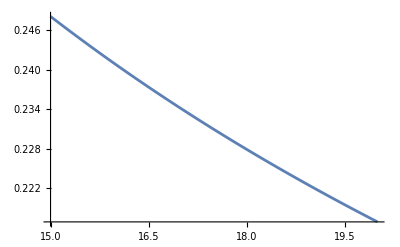

```mathematica
Plot[Gamma[3/2+x]/Gamma[2+x], {x, 15, 20}]
```

```mathematica
f[x_] := Gamma[3/2+x]/Gamma[2+x]
Series[f[z],{z, 0, 1}]
```

(√π)/2+(1/2 (-1+EulerGamma) √π+1/2 √π PolyGamma[0,3/2]) z+O[z]^2

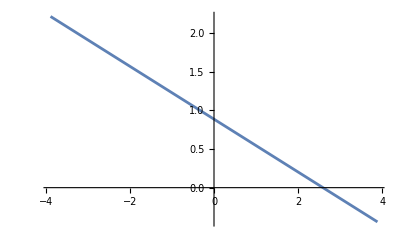

```mathematica
Plot[Evaluate[Normal[(√π)/2+(1/2 (-1+EulerGamma) √π+1/2 √π PolyGamma[0,3/2]) z+O[z]^2]],{z,-3.8830491743431352,3.8830491743431352}]
```

```mathematica
Series[(3 √π)/8,{1,0,5}]
x = x
```

Series::ivar: 1 不是一个有效的变量.

Series[(3 √π)/8,{1,0,5}]

1

```mathematica
Gamma[3/2] 
Gamma[1/2]
```

(√π)/2

√π

```mathematica
(1/N + 2/ N A1 ) (1/N + 2/ N A2 ) // Expand
```

1/N^2+(2 A1)/N^2+(2 A2)/N^2+(4 A1 A2)/N^2

```mathematica
Sum[
Cos[(N-1/2)(k π)/N]*Cos[(i-1/2)*   Pi * k / N ] *  Cos[  Pi * k / N/2 ] ^ (2*t),
{k, 1, N-1}
] + Sum[
Cos[(i-1/2)*   Pi * k / N ] * Cos[  Pi * k / N/2 ] ^ (2*t +1),
{k, 1, N-1}
]
```

```mathematica
∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(1+2 t) Cos[((-1/2+i) k π)/N]+∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(2 t) Cos[((-1/2+i) k π)/N] Cos[(k (-1/2+N) π)/N] //Simplify
```

```mathematica
Cos[(k π)/(2 N)]^(1+2 t) Cos[((-1/2+i) k π)/N]+Cos[(k π)/(2 N)]^(2 t) Cos[((-1/2+i) k π)/N] Cos[(k (-1/2+N) π)/N] //Simplify
```

```mathematica
Cos[(k π)/(2 N)]^(2 t) Cos[((-1/2+i) k π)/N] (Cos[(k π)/(2 N)]+Cos[(k (-1/2+N) π)/N])//TeXForm
```

\left(\cos \left(\frac{\pi  k}{2 N}\right)+\cos \left(\frac{\pi  k \left(N-\frac{1}{2}\right)}{N}\right)\right) \cos \left(\frac{\pi  \left(i-\frac{1}{2}\right) k}{N}\right) \cos ^{2 t}\left(\frac{\pi  k}{2 N}\right)

```mathematica
Cos[(k π)/(2 N)]+Cos[(k (-1/2+N) π)/N] // Simplify
```

```mathematica
Cos[(k π)/(2 N)]+Cos[(k (-1/2+N) π)/N]  // TrigFactor
```

```mathematica
2 Cos[(k π)/(4 N)-(k (-1/2+N) π)/(2 N)] Cos[(k π)/(4 N)+(k (-1/2+N) π)/(2 N)]//TeXForm
```

2 \cos \left(\frac{\pi  k}{4 N}-\frac{\pi  k \left(N-\frac{1}{2}\right)}{2 N}\right) \cos \left(\frac{\pi  k
   \left(N-\frac{1}{2}\right)}{2 N}+\frac{\pi  k}{4 N}\right)

```mathematica
(k π)/(4 N)-(k (-1/2+N) π)/(2 N) //Simplify
```

-(k (-1+N) π)/(2 N)

```mathematica
(k π)/(4 N)+(k (-1/2+N) π)/(2 N)//Simplify
```

(k π)/2

```mathematica
Sum[Cos[((-1/2+i) k π)/N], {i, 1, N}]
```

```mathematica
-1/2 Cos[1/2 (1+2 k) π] Csc[(k π)/(2 N)]//TeXForm
```

-\frac{1}{2} \cos \left(\frac{1}{2} \pi  (2 k+1)\right) \csc \left(\frac{\pi  k}{2 N}\right)

```mathematica
Cos[1/2 (1+2 k) π] // Simplify
```

-Sin[k π]

```mathematica
Cos[(k π)/(2 N)]^(1+2 t) Cos[((-1/2+i) k π)/N] Cos[(j π)/(2 N)]^(2 t) Cos[((-1/2+i) j π)/N] Cos[(j (-1/2+N) π)/N] // Simplify //TeXForm
```

\cos \left(\frac{\pi  j \left(N-\frac{1}{2}\right)}{N}\right) \cos \left(\frac{\pi  \left(i-\frac{1}{2}\right) j}{N}\right) \cos
   \left(\frac{\pi  \left(i-\frac{1}{2}\right) k}{N}\right) \cos ^{2 t}\left(\frac{\pi  j}{2 N}\right) \cos ^{2 t+1}\left(\frac{\pi 
   k}{2 N}\right)

```mathematica
Cos[((-1/2+i) j π)/N]Cos[((-1/2+i) k π)/N]
```

```mathematica
Cos[((-1/2+i) j π)/N] Cos[((-1/2+i) k π)/N] // TrigReduce
```

```mathematica
1/2 (Cos[((-1/2+i) j π)/N-((-1/2+i) k π)/N]+Cos[((-1/2+i) j π)/N+((-1/2+i) k π)/N])//TeXForm
```

\frac{1}{2} \left(\cos \left(\frac{\pi  \left(i-\frac{1}{2}\right) j}{N}-\frac{\pi  \left(i-\frac{1}{2}\right) k}{N}\right)+\cos
   \left(\frac{\pi  \left(i-\frac{1}{2}\right) j}{N}+\frac{\pi  \left(i-\frac{1}{2}\right) k}{N}\right)\right)

```mathematica
Cos[((-1/2+i) j π)/N-((-1/2+i) k π)/N]// Simplify
```

```mathematica
Cos[((-1+2 i) (j-k) π)/(2 N)]//TeXForm
```

\cos \left(\frac{\pi  (2 i-1) (j-k)}{2 N}\right)

```mathematica
Cos[((-1/2+i) j π)/N+((-1/2+i) k π)/N] // Simplify
```

```mathematica
Cos[((-1+2 i) (j+k) π)/(2 N)]//TeXForm
```

\cos \left(\frac{\pi  (2 i-1) (j+k)}{2 N}\right)

```mathematica
Sum[Cos[((-1+2 i) (j-k) π)/(2 N)] + Cos[((-1+2 i) (j+k) π)/(2 N)], {i, 1, N}] //Simplify
Sum[Cos[((-1+2 i) (j-k) π)/(2 N)], {i, 1, N}] //Simplify
```

1/2 (-Csc[((j-k) π)/(2 N)] Sin[(-j+k) π]+Csc[((j+k) π)/(2 N)] Sin[(j+k) π])

-1/2 Csc[((j-k) π)/(2 N)] Sin[(-j+k) π]

```mathematica
1/2 (-Csc[((j-k) π)/(2 N)] Sin[(-j+k) π]+Csc[((j+k) π)/(2 N)] Sin[(j+k) π])//TeXForm
```

\frac{1}{2} \left(\sin (\pi  (j+k)) \csc \left(\frac{\pi  (j+k)}{2 N}\right)-\sin (\pi  (k-j)) \csc \left(\frac{\pi  (j-k)}{2
   N}\right)\right)

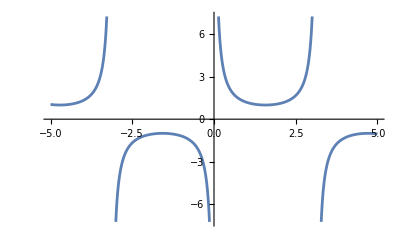

```mathematica
Plot[Csc[x], {x, -5,  5}]
```

```mathematica
Csc[Pi]
```

ComplexInfinity

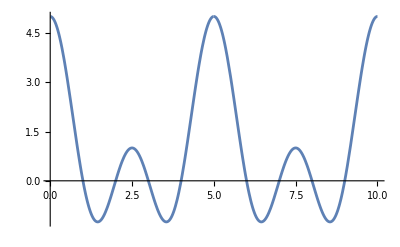

Failure[…]

```mathematica
ComplexInfinity
Plot[Sin[Pi x]Csc[  (Pi x)/5], {x, 0.01, 10}]
```

```mathematica
Sum[
Cos[(k π)/(2 N)]^(1+2 t) Cos[(k π)/(2 N)]^(2 t)  Cos[(k (-1/2+N) π)/N]
,
{k,1,N-1}]
```

```mathematica
∑_(k=1)^(-1+N) Cos[(k π)/(2 N)]^(1+4 t) Cos[(k (-1/2+N) π)/N]// TeXForm
```

\sum _{k=1}^{N-1} \cos \left(\frac{\pi  k \left(N-\frac{1}{2}\right)}{N}\right) \cos ^{4 t+1}\left(\frac{\pi  k}{2 N}\right)